```mathematica
Get["AddedAngle_Alpha/Definitions.m"];
```

Functions investigations

```mathematica
AlphaPrime[0.8,20/180*Pi,-0.2]/Pi*180
```

6.68968

```mathematica
DSumAddedAngleAlpha[500000,Pi/4,Pi/2,0.2,1,{0.8,20/180*Pi,-0.2,AddedAngleScale0}]
```

0.00980028

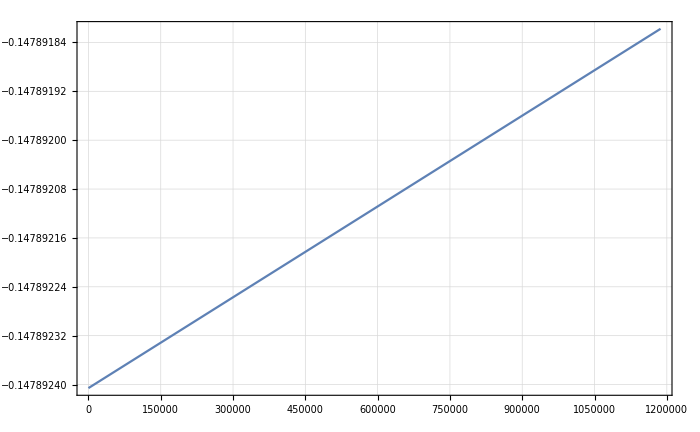

```mathematica
Plot[(DSumAddedAngleAlpha[p,Pi/4,Pi,0.2,1,{0.8,20/180*Pi,-0.2,0.00000001}]-D1stSimple[p,Pi,0.2,Pi/4,1])/D1stSimple[p,Pi,0.2,Pi/4,1],{p,0,1187000}]
```

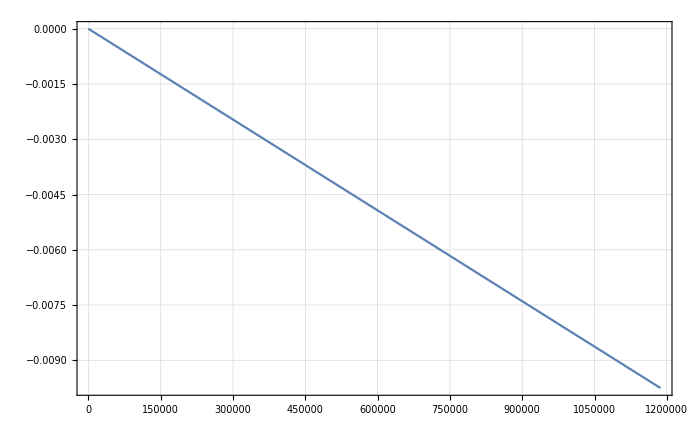

```mathematica
Plot[(DSumAlphaPrime[p,Pi/4,Pi,0.2,1,{0.8,20/180*Pi,-0.2}]-D1stSimple[p,Pi,0.2,Pi/4,1]),{p,0,1187000}]
```

```mathematica
Plot[(DSumAlphaPrime[p,Pi/4,Pi,0.2,1,{0.8,20/180*Pi,-0.2}]-D1stSimple[p,Pi,0.2,Pi/4,1])/D1stSimple[p,Pi,0.2,Pi/4,1],{p,0,1187000}]
```

-Graphics-

```mathematica
Plot[(
DSumAlphaPrime[p,Pi/8,Pi,0.2,1,{0.8,20/180*Pi,-0.2}]-D1stSimple[p,Pi,0.2,Pi/8,1]
)/D1stSimple[p,Pi,0.2,Pi/8,1],{p,0,1187000}]
```

-Graphics-

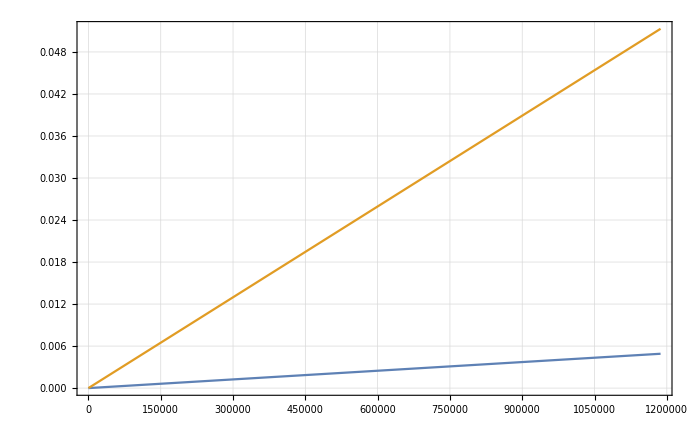

```mathematica
Plot[{
2*D1stSimple[p,AlphaPrime[0.8,20/180*Pi,-0.2],0.2,Pi/4,1],D1stSimple[p,Pi-40/180*Pi,0.2,Pi/4,1]},{p,0,1187000}]
```

```mathematica
Plot[
2*D1stSimple[p,AlphaPrime[0.8,20/180*Pi,-0.2],0.2,Pi/4,1]/D1stSimple[p,Pi-40/180*Pi,0.2,Pi/4,1],{p,0,1187000}]
```

-Graphics-

Transport

```mathematica
Get["AddedAngle_Alpha/Integrand_Transport.m"]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
?pminFuncAlphaPrime
```

Global`pminFuncAlphaPrime

pminFuncAlphaPrime[x0_,xD_,th0_,alpha_,rRxB_,BRxB_,rD_,{R_,AlphaTrans_,zt_}]=(599584916 BRxB √rD (x0-xD) √(1-rRxB Sin[th0]^2))/(2 alpha √rD-4 AlphaTrans √rD-4 √rD ArcSin[R Sin[AlphaTrans]]-alpha √rD rRxB Sin[th0]^2+2 AlphaTrans √rD rRxB Sin[th0]^2+2 √rD rRxB ArcSin[R Sin[AlphaTrans]] Sin[th0]^2+2 rRxB Sin[th0] √(1-rRxB Sin[th0]^2))

```mathematica
pminAlphaPrimeCases[0.,-0.05,Pi/4,Pi,1.,0.2,1.,{0.8,20/180*Pi,-0.2}]
```

1.10589×10^6

```mathematica
pmaxAlphaPrimeCases[0.,-0.05,Pi/4,Pi,1.,0.2,1.,{0.8,20/180*Pi,-0.2}]
```

1.18728×10^6

```mathematica
?IntegrandArithAlphaPrime
```

Global`IntegrandArithAlphaPrime

IntegrandArithAlphaPrime[b_?NumericQ,{xi_?NumericQ,p_?NumericQ,th0_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,x0_?NumericQ,y0_?NumericQ,rA_?NumericQ},{R_,AlphaTrans_,zt_}]:=(ArithApert[xA,yA,xOff,yOff,x0,y0,rG[p,theta2[th0,rA],(rA BRxB)/rRxB]] wmomNormedWb[λ0,κ0,b,p] Sin[th0] WeightrG[xi-x0+DSumAlphaPrime[p,th0,alpha,BRxB,rRxB,{R,AlphaTrans,zt}],p,theta2[th0,rD],(rD BRxB)/rRxB])/(xA+2 rG[pmax,th0,(rA BRxB)/rRxB])

```mathematica
Plot3D[IntegrandArithAlphaPrime[0.,{-0.03,p,th,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,0.,0.,1.},{0.8,20/180*Pi,-0.2}],{th,0,Pi/4},{p,pminAlphaPrimeCases[0.,-0.03,Pi/4,Pi,1.,0.2,1.,{0.8,20/180*Pi,-0.2}],pmaxAlphaPrimeCases[0.,-0.03,Pi/4,Pi,1.,0.2,1.,{0.8,20/180*Pi,-0.2}]}]
```

-Graphics3D-

### compare with no transition region (alphat and zt small)

```mathematica
IntegrandArithAlphaPrime[0.,{-0.03,700000,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,0.,0.,1.},{0.8,20/180*Pi,-0.2}]
```

0.000771744

```mathematica
Plot3D[Re[IntegrandArithAlphaPrime[0.,{-0.03,p,th,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,0.,0.,1.},{0.8,20/180*Pi,-0.2}]-IntegrandArithAlphaPrime[0.,{-0.03,p,th,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,0.,0.,1.},{0.8,0.1/180*Pi,-0.002}]],{th,0,Pi/4},{p,0,pmax},PlotPoints->30]
```

-Graphics3D-

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XDatam55p05=XDataCreation[{-0.055,0.005},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncMemoArith[b_?NumericQ,{alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,y0_?NumericQ,rA_?NumericQ},{R_,AlphaTrans_,zt_},XList_,IntPrec_
]:=
FitFuncMemoArith[b,{alpha,BRxB,rRxB,rD,rF},{xA,yA,xOff,yOff,y0,rA},{R,AlphaTrans,zt},XList,IntPrec]=
Reverse[IntTableArithAlphaPrime[b,{alpha,BRxB,rRxB,rD,rF},{xA,yA,xOff,yOff,y0,rA},{R,AlphaTrans,zt},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormArith[bin_?NumericQ,b_?NumericQ,{alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,y0_?NumericQ,rA_?NumericQ},{R_,AlphaTrans_,zt_},XList_,IntPrec_]:=FitFuncMemoArith[b,{alpha,BRxB,rRxB,rD,rF},{xA,yA,xOff,yOff,y0,rA},{R,AlphaTrans,zt},XList,IntPrec][[bin]]/Total[FitFuncMemoArith[b,{alpha,BRxB,rRxB,rD,rF},{xA,yA,xOff,yOff,y0,rA},{R,AlphaTrans,zt},XList,IntPrec]]
```

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormArith[bin,0.,{Pi/2,0.2,1/2.,1/2.,1.},{0.01,0.035,0.,0.,0.,1/2.},{0.8,10/180*Pi,-0.1},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844535 and 0.00844535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677515 and 0.00677515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511133 and 0.00511133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687313 and 0.000687313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339376 and 0.00608067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22053 and 0.00859308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129216 and 0.00345826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350264 and 0.000384409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.0756 and 0.00311395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26516 and 0.0167029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89216 and 0.0160578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5431 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65721 and 0.0216799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88714 and 0.00989674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539525 for the integral and error estimates.

748.289657

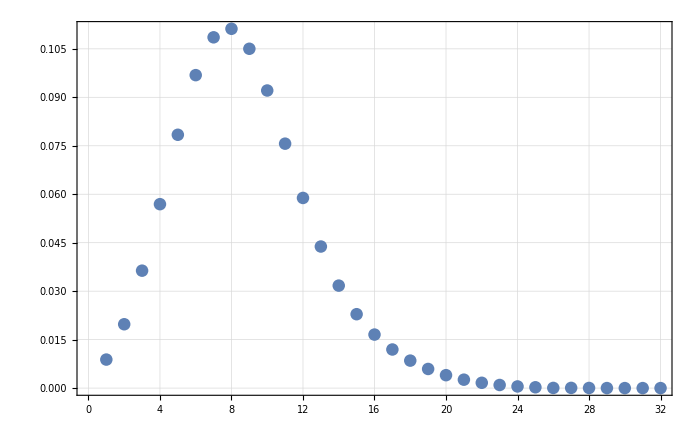

```mathematica
ListPlot[ILLData90noFilter]
```

### 750s

### zero data, no transition

```mathematica
t0=AbsoluteTime[];
ZeroTransitionILLData90noFilter=Table[{bin,FitFuncBinNormArith[bin,0.,{Pi/2,0.2,1/2.,1/2.,1.},{0.01,0.035,0.,0.,0.,1/2.},{0.8,0.001/180*Pi,-0.0001},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.499995,0.844124,0.844124}. NIntegrate obtained 0.0535996 and 0.000588954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0157918 and 0.00411691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0939189 and 0.00245487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.29572 and 0.00596472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.33864 and 0.00585932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.56789 and 0.00567348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 8.31243 and 0.00957819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 5.94892 and 0.0160688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.13161 and 0.0357181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.87958 and 0.00443634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.830343 and 0.0259897 for the integral and error estimates.

1203.58537

### took 1203s

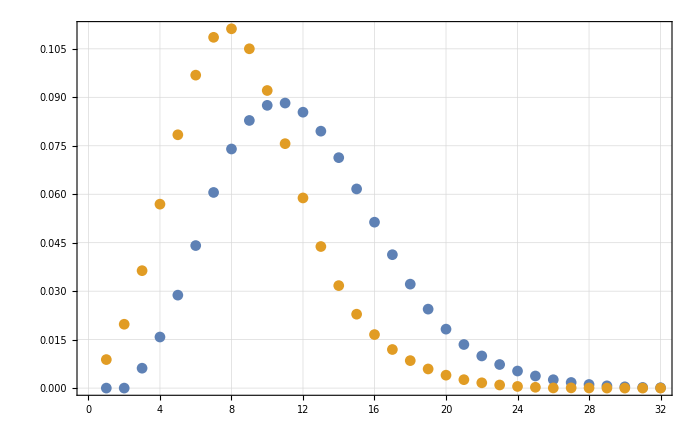

```mathematica
ListPlot[{ZeroTransitionILLData90noFilter,ILLData90noFilter}]
```

Fits

### dR fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dRFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,b,{Pi/2,0.2,1/2.,1/2.,1.},{0.01,0.035,0.,0.,0.,1/2.},{0.8+0.8*10^-4,10/180*Pi,-0.1},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 18:27:48

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677489 and 0.00677489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844831 and 0.00844831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510952 and 0.00510952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686656 and 0.000686656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339323 and 0.00608105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220502 and 0.00859463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129196 and 0.00345704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350223 and 0.000384493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07538 and 0.00311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26483 and 0.0168113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89179 and 0.0160535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88747 and 0.00986433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845178 and 0.00845178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511171 and 0.00511171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068697 and 0.00068697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677772 and 0.00677772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339456 and 0.00608354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129242 and 0.00345846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220577 and 0.00859797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350335 and 0.000384613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.076 and 0.00311293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2657 and 0.0167046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89276 and 0.0160559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5419 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88671 and 0.00988115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65736 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845205 and 0.00845205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686994 and 0.000686994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511188 and 0.00511188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677793 and 0.00677793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339466 and 0.00608373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129246 and 0.00345857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220583 and 0.00859822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350344 and 0.000384623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07604 and 0.00311299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26576 and 0.016705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89283 and 0.016056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5418 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65734 and 0.0217658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88665 and 0.00988104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845162 and 0.00845162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511161 and 0.00511161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677758 and 0.00677758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686955 and 0.000686955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033945 and 0.00608342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12924 and 0.00345839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220574 and 0.00859781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35033 and 0.000384608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07597 and 0.00311289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26566 and 0.0167044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89271 and 0.0160557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.542 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88675 and 0.00988122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65737 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686713 and 0.000686713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510991 and 0.00510991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844894 and 0.00844894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067754 and 0.0067754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339347 and 0.0060815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129204 and 0.00345729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220516 and 0.00859523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350243 and 0.000384515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07549 and 0.0031123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26501 and 0.0167162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89197 and 0.0160539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88731 and 0.00988234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65758 and 0.0217643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677762 and 0.00677762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845166 and 0.00845166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686959 and 0.000686959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511164 and 0.00511164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339451 and 0.00608345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129241 and 0.00345841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220574 and 0.00859785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350331 and 0.000384609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07598 and 0.0031129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26567 and 0.0167045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89273 and 0.0160558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.542 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88674 and 0.0098812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65737 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677238 and 0.00677238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510757 and 0.00510757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686378 and 0.000686378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844523 and 0.00844523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339205 and 0.00607884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129155 and 0.00345577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220435 and 0.00859165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350123 and 0.000384386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07483 and 0.00311148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26414 and 0.0168068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89093 and 0.0160514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5449 and 0.0106293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88812 and 0.00986561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65787 and 0.0217625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677769 and 0.00677769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511169 and 0.00511169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845175 and 0.00845175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686967 and 0.000686967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339455 and 0.00608352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129242 and 0.00345845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220577 and 0.00859794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350334 and 0.000384613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07599 and 0.00311292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2657 and 0.0167046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89275 and 0.0160558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5419 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88672 and 0.00988116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65736 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844651 and 0.00844651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510838 and 0.00510838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677343 and 0.00677343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686494 and 0.000686494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339254 and 0.00607975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129172 and 0.00345629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220463 and 0.00859289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350164 and 0.00038443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07506 and 0.00311176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26443 and 0.0168086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89129 and 0.0160523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5443 and 0.0106291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88785 and 0.00986508 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65777 and 0.0217631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051074 and 0.0051074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844497 and 0.00844497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686354 and 0.000686354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677217 and 0.00677217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339195 and 0.00607865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129151 and 0.00345566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220429 and 0.0085914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350114 and 0.000384377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07478 and 0.00311142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26408 and 0.0168064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89086 and 0.0160512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.545 and 0.0106294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88818 and 0.00986572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65789 and 0.0217624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068697 and 0.00068697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677772 and 0.00677772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845178 and 0.00845178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511171 and 0.00511171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339456 and 0.00608354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129242 and 0.00345846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220577 and 0.00859797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350335 and 0.000384613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.076 and 0.00311293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2657 and 0.0167046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89276 and 0.0160559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5419 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88671 and 0.00988115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65736 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510814 and 0.00510814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068646 and 0.00068646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844613 and 0.00844613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677312 and 0.00677312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033924 and 0.00607949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220455 and 0.00859253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129167 and 0.00345614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350152 and 0.000384417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07499 and 0.00311168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26434 and 0.0168081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89118 and 0.016052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5445 and 0.0106291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6578 and 0.0217629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88793 and 0.00986524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677548 and 0.00677548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686722 and 0.000686722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510998 and 0.00510998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844904 and 0.00844904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339351 and 0.00608157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129206 and 0.00345733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220518 and 0.00859533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350246 and 0.000384518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07551 and 0.00311232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.0167163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.892 and 0.016054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0098823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65757 and 0.0217643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844829 and 0.00844829 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677487 and 0.00677487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051095 and 0.0051095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686654 and 0.000686654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339322 and 0.00608103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129195 and 0.00345702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220501 and 0.0085946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350222 and 0.000384492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07537 and 0.00311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26483 and 0.0168112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89179 and 0.0160535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88747 and 0.00986434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686947 and 0.000686947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511155 and 0.00511155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677751 and 0.00677751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845153 and 0.00845153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339447 and 0.00608336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220572 and 0.00859773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129239 and 0.00345836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350327 and 0.000384605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07595 and 0.00311287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26565 and 0.0167043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89269 and 0.0160557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.542 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88676 and 0.00988126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65738 and 0.0217655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.006778 and 0.006778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687001 and 0.000687001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511193 and 0.00511193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845213 and 0.00845213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339469 and 0.00608378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220585 and 0.0085983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129247 and 0.0034586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350346 and 0.000384625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07606 and 0.00311301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26578 and 0.0167051 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89286 and 0.0160561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5418 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88664 and 0.00988101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65733 and 0.0217658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844855 and 0.00844855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677508 and 0.00677508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510967 and 0.00510967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686678 and 0.000686678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339332 and 0.00608122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129199 and 0.00345713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220507 and 0.00859485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35023 and 0.000384501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07542 and 0.00311222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26489 and 0.0168116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89186 and 0.0160537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5434 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88739 and 0.0098825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65761 and 0.0217641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677251 and 0.00677251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686392 and 0.000686392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844538 and 0.00844538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510766 and 0.00510766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339211 and 0.00607895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220438 and 0.0085918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129157 and 0.00345583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350128 and 0.000384391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07486 and 0.00311152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26417 and 0.016807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89097 and 0.0160515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5448 and 0.0106293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88809 and 0.00986555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65785 and 0.0217626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677641 and 0.00677641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845018 and 0.00845018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051107 and 0.0051107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686825 and 0.000686825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339395 and 0.00608238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129221 and 0.0034578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220542 and 0.00859642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350283 and 0.000384558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07571 and 0.00311257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26529 and 0.016718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89231 and 0.0160548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5426 and 0.0106286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88705 and 0.00988182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65748 and 0.0217649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686341 and 0.000686341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510731 and 0.00510731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844482 and 0.00844482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677205 and 0.00677205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033919 and 0.00607854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129149 and 0.0034556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220426 and 0.00859126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350109 and 0.000384371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07476 and 0.00311139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26404 and 0.0168062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89082 and 0.0160511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5451 and 0.0106294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88821 and 0.00986578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6579 and 0.0217623 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511106 and 0.00511106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677687 and 0.00677687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845074 and 0.00845074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686876 and 0.000686876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339416 and 0.00608279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129228 and 0.00345803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220555 and 0.00859697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350302 and 0.000384577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07581 and 0.0031127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26541 and 0.0167188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89247 and 0.0160551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0106286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88693 and 0.00988159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65744 and 0.0217651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677571 and 0.00677571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844932 and 0.00844932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686747 and 0.000686747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511015 and 0.00511015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339362 and 0.00608177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129209 and 0.00345745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220524 and 0.00859559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350255 and 0.000384528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07556 and 0.00311238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26509 and 0.0167167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89207 and 0.0160542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88723 and 0.00988218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65755 and 0.0217645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677379 and 0.00677379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510866 and 0.00510866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686534 and 0.000686534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844696 and 0.00844696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339272 and 0.00608008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129178 and 0.00345648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220473 and 0.00859332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350179 and 0.000384446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07514 and 0.00311186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26453 and 0.0168093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89142 and 0.0160526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5441 and 0.010629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88775 and 0.00986489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677488 and 0.00677488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686655 and 0.000686655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510951 and 0.00510951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084483 and 0.0084483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339323 and 0.00608104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129196 and 0.00345703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220502 and 0.00859461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350222 and 0.000384492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07538 and 0.00311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26483 and 0.0168112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89179 and 0.0160535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88747 and 0.00986434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511042 and 0.00511042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686786 and 0.000686786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677606 and 0.00677606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844974 and 0.00844974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339378 and 0.00608207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129215 and 0.00345762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220533 and 0.00859601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350269 and 0.000384543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07563 and 0.00311248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26519 and 0.0167174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89219 and 0.0160545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88714 and 0.009882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65752 and 0.0217647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844966 and 0.00844966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686778 and 0.000686778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677599 and 0.00677599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511037 and 0.00511037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339375 and 0.00608202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129214 and 0.00345759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220531 and 0.00859593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350266 and 0.00038454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07562 and 0.00311246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26517 and 0.0167172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89217 and 0.0160544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88716 and 0.00988204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65752 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845044 and 0.00845044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686848 and 0.000686848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511086 and 0.00511086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677662 and 0.00677662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339405 and 0.00608257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129224 and 0.00345791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220548 and 0.00859667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350292 and 0.000384567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07576 and 0.00311263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26535 and 0.0167183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89239 and 0.0160549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5425 and 0.0106286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65746 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88699 and 0.00988171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686638 and 0.000686638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510939 and 0.00510939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677473 and 0.00677473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844811 and 0.00844811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339315 and 0.0060809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129193 and 0.00345695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220498 and 0.00859443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350216 and 0.000384486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07534 and 0.00311212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26479 and 0.016811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89174 and 0.0160534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5436 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88751 and 0.00986442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.0217639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677765 and 0.00677765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511166 and 0.00511166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686962 and 0.000686962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084517 and 0.0084517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339453 and 0.00608348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129241 and 0.00345843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220575 and 0.00859789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350333 and 0.000384611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07598 and 0.00311291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26568 and 0.0167045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89274 and 0.0160558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.542 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88673 and 0.00988119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65736 and 0.0217656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511045 and 0.00511045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677609 and 0.00677609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844978 and 0.00844978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686789 and 0.000686789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033938 and 0.0060821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129215 and 0.00345764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00859604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35027 and 0.000384544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07564 and 0.00311249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2652 and 0.0167174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8922 and 0.0160545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88713 and 0.00988199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65751 and 0.0217647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067779 and 0.0067779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068699 and 0.00068699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845201 and 0.00845201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511186 and 0.00511186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339465 and 0.0060837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129245 and 0.00345856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220582 and 0.00859819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350343 and 0.000384621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07604 and 0.00311298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26575 and 0.016705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89282 and 0.016056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5418 and 0.0106285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65734 and 0.0217657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88666 and 0.00988106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00540381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067762 and 0.0067762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511053 and 0.00511053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844992 and 0.00844992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686802 and 0.000686802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339385 and 0.0060822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129217 and 0.0034577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220537 and 0.00859617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350275 and 0.000384549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07567 and 0.00311252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26523 and 0.0167176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89224 and 0.0160546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8871 and 0.00988193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6575 and 0.0217647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511118 and 0.00511118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845094 and 0.00845094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686893 and 0.000686893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677703 and 0.00677703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339424 and 0.00608293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129231 and 0.00345811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220559 and 0.00859715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350308 and 0.000384584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07585 and 0.00311274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26546 and 0.0167191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89252 and 0.0160553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5423 and 0.0106286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88689 and 0.00988151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65742 and 0.0217652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0054036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686713 and 0.000686713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844894 and 0.00844894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510991 and 0.00510991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067754 and 0.0067754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339347 and 0.00608149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129204 and 0.00345729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220515 and 0.00859523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350243 and 0.000384515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07549 and 0.0031123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26501 and 0.0167162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89197 and 0.0160539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88731 and 0.00988234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65758 and 0.0217643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511066 and 0.00511066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068682 and 0.00068682 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845012 and 0.00845012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677636 and 0.00677636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339393 and 0.00608234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12922 and 0.00345778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220541 and 0.00859637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350281 and 0.000384556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.0757 and 0.00311256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26527 and 0.0167179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8923 and 0.0160547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5427 and 0.0106286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65749 and 0.0217648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88706 and 0.00988185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510971 and 0.00510971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844862 and 0.00844862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677514 and 0.00677514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686684 and 0.000686684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339335 and 0.00608127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220509 and 0.00859492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.1292 and 0.00345716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350233 and 0.000384503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07543 and 0.00311223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2649 and 0.0168117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89188 and 0.0160537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5434 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88738 and 0.00988247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6576 and 0.0217641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844832 and 0.00844832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677489 and 0.00677489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686657 and 0.000686657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510952 and 0.00510952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339323 and 0.00608105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129196 and 0.00345704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220502 and 0.00859463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350223 and 0.000384493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07538 and 0.00311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26483 and 0.0168113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89179 and 0.0160535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88747 and 0.00986433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686621 and 0.000686621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677457 and 0.00677457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844792 and 0.00844792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510927 and 0.00510927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339308 and 0.00608077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129191 and 0.00345687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220493 and 0.00859425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35021 and 0.000384479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07531 and 0.00311208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26474 and 0.0168107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89168 and 0.0160532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0106289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.88755 and 0.0098645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65766 and 0.0217638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.0053982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844975 and 0.00844975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511043 and 0.00511043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686786 and 0.000686786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677606 and 0.00677606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339378 and 0.00608208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129215 and 0.00345763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220533 and 0.00859601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350269 and 0.000384543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07564 and 0.00311248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26519 and 0.0167174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89219 and 0.0160545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65751 and 0.0217647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88714 and 0.009882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511037 and 0.00511037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677599 and 0.00677599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686778 and 0.000686778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844966 and 0.00844966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339375 and 0.00608202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220531 and 0.00859593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129214 and 0.00345759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350266 and 0.00038454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07562 and 0.00311246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26517 and 0.0167172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89217 and 0.0160544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0106287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88716 and 0.00988204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65752 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18706 and 0.00539855 for the integral and error estimates.

28363.11937

### took 28363s or 7.9h

```mathematica
dRFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000614815 | 0.0000512838 | -11.9885 | 3.56477×10^-13

```mathematica
dRFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-6.14815

### TransAlpha fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dTAFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,b,{Pi/2,0.2,1/2.,1/2.,1.},{0.01,0.035,0.,0.,0.,1/2.},{0.8,10/180*Pi+10/180*Pi*10^-4,-0.1},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Sat 29 Jun 2019 02:20:31

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677383 and 0.00677383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084519 and 0.0084519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510743 and 0.00510743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685868 and 0.000685868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339261 and 0.00608108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220481 and 0.00857591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129174 and 0.00345564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350178 and 0.000384644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07513 and 0.00310879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26448 and 0.0166914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89139 and 0.0160767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.544 and 0.0107146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88781 and 0.00991663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65789 and 0.0217634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677665 and 0.00677665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510962 and 0.00510962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845537 and 0.00845537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686181 and 0.000686181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339394 and 0.00608357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220556 and 0.00857925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12922 and 0.00345707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35029 and 0.000384763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07574 and 0.00310521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26526 and 0.0166964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89236 and 0.016079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88708 and 0.00991517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65762 and 0.0217651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677687 and 0.00677687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510979 and 0.00510979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686205 and 0.000686205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845563 and 0.00845563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339404 and 0.00608376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129224 and 0.00345718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220562 and 0.0085795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350299 and 0.000384772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07579 and 0.00310527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26532 and 0.0166968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89244 and 0.0160792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5422 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88702 and 0.00991506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6576 and 0.0217652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510952 and 0.00510952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084552 and 0.0084552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686166 and 0.000686166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677652 and 0.00677652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339387 and 0.00608345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129218 and 0.003457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220553 and 0.00857909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350285 and 0.000384757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07571 and 0.00310517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26522 and 0.0166962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89232 and 0.0160789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88712 and 0.00991524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.0053903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677434 and 0.00677434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845252 and 0.00845252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510782 and 0.00510782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685925 and 0.000685925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339285 and 0.00608153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220495 and 0.00857651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129182 and 0.0034559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350198 and 0.000384665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07524 and 0.00310459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26462 and 0.0166923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89157 and 0.0160771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0107145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88768 and 0.00991637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65784 and 0.0217637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845525 and 0.00845525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510954 and 0.00510954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677655 and 0.00677655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068617 and 0.00068617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339389 and 0.00608348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220554 and 0.00857913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129219 and 0.00345702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350286 and 0.000384759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07572 and 0.00310518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26523 and 0.0166963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89233 and 0.0160789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88711 and 0.00991522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068559 and 0.00068559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677132 and 0.00677132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510548 and 0.00510548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844881 and 0.00844881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339143 and 0.00607887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220414 and 0.00857294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129133 and 0.00345437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350078 and 0.000384537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07458 and 0.00310811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26378 and 0.016687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89053 and 0.0160746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5454 and 0.0107151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88846 and 0.00993468 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65813 and 0.0217619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677663 and 0.00677663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686179 and 0.000686179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845534 and 0.00845534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051096 and 0.0051096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339393 and 0.00608355 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12922 and 0.00345706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220556 and 0.00857922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350289 and 0.000384762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07574 and 0.0031052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26525 and 0.0166964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89235 and 0.016079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88709 and 0.00991518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677236 and 0.00677236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845009 and 0.00845009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510629 and 0.00510629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685706 and 0.000685706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339192 and 0.00607979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12915 and 0.0034549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220442 and 0.00857417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350119 and 0.000384581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07481 and 0.00310839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26407 and 0.0166888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89089 and 0.0160754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5448 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88819 and 0.00993415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65803 and 0.0217625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510531 and 0.00510531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677111 and 0.00677111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844855 and 0.00844855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685567 and 0.000685567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339133 and 0.00607868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129129 and 0.00345427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220409 and 0.00857269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350069 and 0.000384528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07454 and 0.00310805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26372 and 0.0166866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89046 and 0.0160744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5455 and 0.0107151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88852 and 0.00993479 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65815 and 0.0217618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845537 and 0.00845537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686181 and 0.000686181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510962 and 0.00510962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677665 and 0.00677665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339394 and 0.00608357 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12922 and 0.00345707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220556 and 0.00857925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35029 and 0.000384763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07574 and 0.00310521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26526 and 0.0166964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89236 and 0.016079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88708 and 0.00991517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65762 and 0.0217651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677206 and 0.00677206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844972 and 0.00844972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510605 and 0.00510605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685672 and 0.000685672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339177 and 0.00607952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220434 and 0.00857381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129145 and 0.00345475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350107 and 0.000384568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07474 and 0.00310831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26399 and 0.0166883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89079 and 0.0160752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.545 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88827 and 0.0099343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65806 and 0.0217623 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845262 and 0.00845262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510789 and 0.00510789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685934 and 0.000685934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677442 and 0.00677442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339289 and 0.0060816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129184 and 0.00345594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220497 and 0.00857661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350201 and 0.000384669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07526 and 0.00310461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26464 and 0.0166925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8916 and 0.0160772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88766 and 0.00991632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65784 and 0.0217637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845187 and 0.00845187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685866 and 0.000685866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510741 and 0.00510741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677381 and 0.00677381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033926 and 0.00608106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220481 and 0.00857588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129173 and 0.00345563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350177 and 0.000384643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07513 and 0.00310878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26447 and 0.0166914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89139 and 0.0160767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.544 and 0.0107146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88782 and 0.00991664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6579 and 0.0217634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845512 and 0.00845512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677645 and 0.00677645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686159 and 0.000686159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510946 and 0.00510946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339384 and 0.00608339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129217 and 0.00345697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220551 and 0.00857901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350282 and 0.000384755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.0757 and 0.00310515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2652 and 0.0166961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89229 and 0.0160789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5425 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88713 and 0.00991528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.0217649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686212 and 0.000686212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677693 and 0.00677693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845571 and 0.00845571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510984 and 0.00510984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339407 and 0.00608381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129225 and 0.00345721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220564 and 0.00857958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350301 and 0.000384775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07581 and 0.00310528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26534 and 0.0166969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89246 and 0.0160793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5422 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88701 and 0.00991503 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6576 and 0.0217652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068589 and 0.00068589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845213 and 0.00845213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677402 and 0.00677402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510758 and 0.00510758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033927 and 0.00608125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129177 and 0.00345574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220486 and 0.00857614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350185 and 0.000384652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07517 and 0.00310884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26453 and 0.0166918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89146 and 0.0160768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5439 and 0.0107145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88777 and 0.00991653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65788 and 0.0217635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677144 and 0.00677144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510558 and 0.00510558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685604 and 0.000685604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844896 and 0.00844896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339149 and 0.00607898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220418 and 0.00857309 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129135 and 0.00345444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350083 and 0.000384542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07461 and 0.00310814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26382 and 0.0166872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89058 and 0.0160747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5453 and 0.010715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88843 and 0.00993462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65812 and 0.021762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686036 and 0.000686036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510861 and 0.00510861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845376 and 0.00845376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677534 and 0.00677534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339332 and 0.00608242 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129199 and 0.00345641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220522 and 0.0085777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350238 and 0.000384708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07546 and 0.00310486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2649 and 0.0166941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89191 and 0.0160779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0107143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88742 and 0.00991585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65775 and 0.0217643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.0053852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084484 and 0.0084484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685553 and 0.000685553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677099 and 0.00677099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510522 and 0.00510522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339127 and 0.00607857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129127 and 0.00345421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220406 and 0.00857255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350064 and 0.000384523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07451 and 0.00310802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26369 and 0.0166864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89042 and 0.0160743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5456 and 0.0107151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88855 and 0.00993485 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65817 and 0.0217617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677453 and 0.00677453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510797 and 0.00510797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685946 and 0.000685946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845276 and 0.00845276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339294 and 0.00608169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.2205 and 0.00857673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129185 and 0.00345599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350206 and 0.000384673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07528 and 0.00310464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26467 and 0.0166927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89163 and 0.0160773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5436 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88763 and 0.00991627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65783 and 0.0217638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685785 and 0.000685785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845097 and 0.00845097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510684 and 0.00510684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677307 and 0.00677307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339225 and 0.00608041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129161 and 0.00345526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220461 and 0.00857502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350148 and 0.000384612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07497 and 0.00310858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26427 and 0.0166901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89114 and 0.016076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5444 and 0.0107147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88801 and 0.00993378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65797 and 0.0217629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677486 and 0.00677486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510823 and 0.00510823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845316 and 0.00845316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685983 and 0.000685983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339309 and 0.00608199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220509 and 0.00857713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129191 and 0.00345616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350219 and 0.000384687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07535 and 0.00310473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26476 and 0.0166933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89175 and 0.0160775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5434 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88755 and 0.0099161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6578 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510945 and 0.00510945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686157 and 0.000686157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677643 and 0.00677643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084551 and 0.0084551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339383 and 0.00608338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220551 and 0.00857899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129217 and 0.00345696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350282 and 0.000384754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.0757 and 0.00310515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2652 and 0.0166961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89229 and 0.0160788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5425 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88714 and 0.00991528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.0217649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677266 and 0.00677266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510652 and 0.00510652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845046 and 0.00845046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685738 and 0.000685738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339206 and 0.00608005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129155 and 0.00345505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22045 and 0.00857452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350131 and 0.000384594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07488 and 0.00310847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26415 and 0.0166894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89099 and 0.0160757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5447 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65801 and 0.0217627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88811 and 0.00993399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677446 and 0.00677446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845267 and 0.00845267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510792 and 0.00510792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685938 and 0.000685938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033929 and 0.00608163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129184 and 0.00345596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220498 and 0.00857665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350203 and 0.00038467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07526 and 0.00310462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26465 and 0.0166926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89161 and 0.0160772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88765 and 0.0099163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65783 and 0.0217638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510971 and 0.00510971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677677 and 0.00677677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686194 and 0.000686194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845551 and 0.00845551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339399 and 0.00608367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129222 and 0.00345713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220559 and 0.00857938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350295 and 0.000384768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07577 and 0.00310524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26529 and 0.0166966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8924 and 0.0160791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5423 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88705 and 0.00991511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65761 and 0.0217651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067768 and 0.0067768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845555 and 0.00845555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510974 and 0.00510974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686197 and 0.000686197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339401 and 0.0060837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129223 and 0.00345714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22056 and 0.00857942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350296 and 0.000384769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07578 and 0.00310525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2653 and 0.0166967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89241 and 0.0160792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5423 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88704 and 0.0099151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65761 and 0.0217651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510787 and 0.00510787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685931 and 0.000685931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084526 and 0.0084526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067744 and 0.0067744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339288 and 0.00608158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220496 and 0.00857658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129183 and 0.00345593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.3502 and 0.000384668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07525 and 0.0031046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26463 and 0.0166924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89159 and 0.0160771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88767 and 0.00991634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65784 and 0.0217637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686174 and 0.000686174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845529 and 0.00845529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510957 and 0.00510957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677658 and 0.00677658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033939 and 0.00608351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220555 and 0.00857917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129219 and 0.00345703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350288 and 0.00038476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07573 and 0.00310519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26524 and 0.0166963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89234 and 0.016079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8871 and 0.00991521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65763 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845298 and 0.00845298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510812 and 0.00510812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685966 and 0.000685966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677471 and 0.00677471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339302 and 0.00608186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129188 and 0.00345609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220505 and 0.00857695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350213 and 0.000384681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07532 and 0.00310469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26472 and 0.016693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8917 and 0.0160774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0107144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88758 and 0.00991617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65781 and 0.0217639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677648 and 0.00677648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510949 and 0.00510949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845515 and 0.00845515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686162 and 0.000686162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339385 and 0.00608341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129217 and 0.00345698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220552 and 0.00857904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350283 and 0.000384756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07571 and 0.00310516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26521 and 0.0166961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8923 and 0.0160789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5425 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88713 and 0.00991526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510949 and 0.00510949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845516 and 0.00845516 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677648 and 0.00677648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686163 and 0.000686163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129217 and 0.00345698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339386 and 0.00608342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220552 and 0.00857905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350284 and 0.000384756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07571 and 0.00310516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26521 and 0.0166961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89231 and 0.0160789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5425 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88712 and 0.00991526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65764 and 0.021765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00539029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845234 and 0.00845234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510771 and 0.00510771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685909 and 0.000685909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677419 and 0.00677419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339278 and 0.0060814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12918 and 0.00345583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220491 and 0.00857634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350192 and 0.000384659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07521 and 0.00310455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26458 and 0.0166921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89152 and 0.016077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5438 and 0.0107145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88772 and 0.00991644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65786 and 0.0217636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.0053849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845158 and 0.00845158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068584 and 0.00068584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677357 and 0.00677357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510723 and 0.00510723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339249 and 0.00608086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12917 and 0.00345551 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220474 and 0.00857561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350168 and 0.000384633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07508 and 0.00310872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26441 and 0.016691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89131 and 0.0160765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5442 and 0.0107146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88788 and 0.00991676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65792 and 0.0217632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685818 and 0.000685818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510708 and 0.00510708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677338 and 0.00677338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845134 and 0.00845134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.033924 and 0.00608068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129166 and 0.00345541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220469 and 0.00857537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35016 and 0.000384624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07503 and 0.00310866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26435 and 0.0166906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89124 and 0.0160763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5443 and 0.0107147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88793 and 0.00991686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65794 and 0.0217631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.0053847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051065 and 0.0051065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685736 and 0.000685736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845043 and 0.00845043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677263 and 0.00677263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339205 and 0.00608003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129154 and 0.00345504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220449 and 0.0085745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35013 and 0.000384593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07487 and 0.00310846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26415 and 0.0166893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89098 and 0.0160757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5447 and 0.0107148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88812 and 0.009934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65801 and 0.0217627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510827 and 0.00510827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000685988 and 0.000685988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677491 and 0.00677491 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845323 and 0.00845323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339312 and 0.00608203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129192 and 0.00345619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22051 and 0.00857719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350221 and 0.000384689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07536 and 0.00310474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26478 and 0.0166934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89177 and 0.0160776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5434 and 0.0107143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88753 and 0.00991607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65779 and 0.021764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00401276 and 0.00401276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000379877 and 0.000379877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00505728 and 0.00505728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00296294 and 0.00296294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0209335 and 0.00364979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0837649 and 0.00206251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.146966 and 0.00531241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.240036 and 0.000265935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.49938 and 0.0119579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.94441 and 0.0140221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 6.84664 and 0.00708428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 11.6534 and 0.0118298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 13.9625 and 0.0155359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 8.85883 and 0.00890367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.93084 and 0.00956053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 1.1875 and 0.00470857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00505728 and 0.00505728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00296294 and 0.00296294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00401276 and 0.00401276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000379877 and 0.000379877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0209335 and 0.00364979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0837649 and 0.00206251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.146966 and 0.00531241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.240036 and 0.000265935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.49938 and 0.0119579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.94441 and 0.0140221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 6.84664 and 0.00708428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 11.6534 and 0.0118298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 13.9625 and 0.0155359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 8.85883 and 0.00890367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.93084 and 0.00956053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 1.1875 and 0.00470857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00249301 and 0.00249301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0034079 and 0.0034079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00431355 and 0.00431355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000312845 and 0.000312845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0180868 and 0.00311568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0738263 and 0.00175576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.13089 and 0.0045093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.215919 and 0.000239066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.33124 and 0.0104222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.73573 and 0.0134693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 6.61299 and 0.00682655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 11.4931 and 0.0120391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 13.9249 and 0.0240092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.98871 and 0.0097517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000312845 and 0.000312845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0034079 and 0.0034079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00249301 and 0.00249301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00431355 and 0.00431355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0180868 and 0.00311568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0738263 and 0.00175576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.13089 and 0.0045093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.215919 and 0.000239066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.33124 and 0.0104222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.73573 and 0.0134693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 6.61299 and 0.00682655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 11.4931 and 0.0120391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 13.9249 and 0.0240092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.98871 and 0.0097517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845405 and 0.00845405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686062 and 0.000686062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677558 and 0.00677558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510879 and 0.00510879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339343 and 0.00608262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129203 and 0.00345653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220528 and 0.00857798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350247 and 0.000384718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07551 and 0.00310492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0166945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89199 and 0.0160781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88736 and 0.00991573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.65773 and 0.0217644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686095 and 0.000686095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677588 and 0.00677588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510902 and 0.00510902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845442 and 0.00845442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339357 and 0.00608288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220536 and 0.00857833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350259 and 0.00038473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.003105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26505 and 0.0166951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8921 and 0.0160784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88728 and 0.00991557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510902 and 0.00510902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845442 and 0.00845442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677588 and 0.00677588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686095 and 0.000686095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339357 and 0.00608288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220536 and 0.00857833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350259 and 0.00038473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.003105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26505 and 0.0166951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8921 and 0.0160784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88728 and 0.00991557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845435 and 0.00845435 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677582 and 0.00677582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686089 and 0.000686089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8873 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677582 and 0.00677582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686089 and 0.000686089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845435 and 0.00845435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8873 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845435 and 0.00845435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677582 and 0.00677582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8873 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677582 and 0.00677582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845435 and 0.00845435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8873 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510899 and 0.00510899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845437 and 0.00845437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686091 and 0.000686091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677584 and 0.00677584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07557 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.00991559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0107149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677583 and 0.00677583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510898 and 0.00510898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068609 and 0.00068609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00845436 and 0.00845436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339355 and 0.00608284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129207 and 0.00345665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00857827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 3.07556 and 0.00310499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26503 and 0.016695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89208 and 0.0160783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0107142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88729 and 0.0099156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 2.6577 and 0.0217646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18722 and 0.00538532 for the integral and error estimates.

91166.800475

### took 91166 s or 25h

```mathematica
dTAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.00120256 | 0.0000692609 | -17.3628 | 1.5911×10^-17

```mathematica
dTAFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-12.0256

## zt Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dztFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,b,{Pi/2,0.2,1/2.,1/2.,1.},{0.01,0.035,0.,0.,0.,1/2.},{0.8,10/180*Pi,-0.1+0.1*10^-4},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Sun 30 Jun 2019 14:11:21

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.006775 and 0.006775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511121 and 0.00511121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687296 and 0.000687296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844517 and 0.00844517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339369 and 0.00608054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129214 and 0.00345819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220526 and 0.0085929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350258 and 0.000384402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07556 and 0.00311391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26512 and 0.0167026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8921 and 0.0160577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88718 and 0.00989682 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65722 and 0.0216798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511341 and 0.00511341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677782 and 0.00677782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687609 and 0.000687609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844863 and 0.00844863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339502 and 0.00608302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12926 and 0.00345961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220602 and 0.00859624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35037 and 0.000384523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07618 and 0.00311467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2659 and 0.0167076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89307 and 0.0160601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5416 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88645 and 0.00989537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65695 and 0.0216815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.0054007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677804 and 0.00677804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0084489 and 0.0084489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687633 and 0.000687633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511357 and 0.00511357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339512 and 0.00608321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129264 and 0.00345972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220607 and 0.0085965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350379 and 0.000384532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07623 and 0.00311473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26596 and 0.016708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89315 and 0.0160602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5415 and 0.0106419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88639 and 0.00989526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65693 and 0.0216816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00540076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051133 and 0.0051133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677769 and 0.00677769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687594 and 0.000687594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844847 and 0.00844847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339496 and 0.0060829 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220598 and 0.00859608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129258 and 0.00345954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350365 and 0.000384517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07615 and 0.00311464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26587 and 0.0167074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89303 and 0.0160599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5417 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65697 and 0.0216814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88648 and 0.00989544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00540067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844579 and 0.00844579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687352 and 0.000687352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677551 and 0.00677551 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511161 and 0.00511161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339393 and 0.00608099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129222 and 0.00345844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22054 and 0.0085935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350278 and 0.000384424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07567 and 0.00311404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26526 and 0.0167035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89228 and 0.0160581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5429 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88705 and 0.00989656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65717 and 0.0216801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844851 and 0.00844851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677773 and 0.00677773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511333 and 0.00511333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687598 and 0.000687598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339497 and 0.00608294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220599 and 0.00859613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129258 and 0.00345956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350367 and 0.000384518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07616 and 0.00311465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26588 and 0.0167075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89304 and 0.01606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5416 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88647 and 0.00989542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65696 and 0.0216814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00540068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510926 and 0.00510926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687017 and 0.000687017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844208 and 0.00844208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677249 and 0.00677249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339251 and 0.00607832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129172 and 0.00345692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22046 and 0.00858993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350158 and 0.000384295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07501 and 0.00311322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26442 and 0.0166982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89124 and 0.0160556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5446 and 0.0106429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88783 and 0.00989811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65746 and 0.0216782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.0053946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067778 and 0.0067778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511339 and 0.00511339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844861 and 0.00844861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687607 and 0.000687607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339501 and 0.006083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12926 and 0.0034596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220601 and 0.00859622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35037 and 0.000384522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07618 and 0.00311467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2659 and 0.0167076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89306 and 0.01606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5416 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88645 and 0.00989538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65696 and 0.0216815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.0054007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687133 and 0.000687133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677353 and 0.00677353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511007 and 0.00511007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844336 and 0.00844336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.03393 and 0.00607924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220487 and 0.00859116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12919 and 0.00345744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350199 and 0.00038434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07524 and 0.00311351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26471 and 0.0167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8916 and 0.0160565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.544 and 0.0106427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88756 and 0.00989758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65736 and 0.0216789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051091 and 0.0051091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677228 and 0.00677228 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844182 and 0.00844182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686993 and 0.000686993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339241 and 0.00607814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129169 and 0.00345681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220454 and 0.00858967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350149 and 0.000384286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07497 and 0.00311317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26437 and 0.0166978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89117 and 0.0160554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5447 and 0.010643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88789 and 0.00989822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65748 and 0.0216781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677782 and 0.00677782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511341 and 0.00511341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687609 and 0.000687609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844863 and 0.00844863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339502 and 0.00608302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12926 and 0.00345961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220602 and 0.00859624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35037 and 0.000384523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07618 and 0.00311467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2659 and 0.0167076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89307 and 0.0160601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5416 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88645 and 0.00989537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65695 and 0.0216815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.0054007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844299 and 0.00844299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677323 and 0.00677323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687099 and 0.000687099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510983 and 0.00510983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339286 and 0.00607897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220479 and 0.0085908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129184 and 0.00345729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350187 and 0.000384327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07518 and 0.00311342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26463 and 0.0166995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8915 and 0.0160562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5442 and 0.0106428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88764 and 0.00989773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65739 and 0.0216787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844589 and 0.00844589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511167 and 0.00511167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677559 and 0.00677559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687361 and 0.000687361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339397 and 0.00608106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129223 and 0.00345848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220542 and 0.0085936 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350281 and 0.000384427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07569 and 0.00311407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26528 and 0.0167037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89231 and 0.0160582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88703 and 0.00989652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65717 and 0.0216801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051112 and 0.0051112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844514 and 0.00844514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687293 and 0.000687293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677498 and 0.00677498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339368 and 0.00608052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129213 and 0.00345817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220526 and 0.00859287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350257 and 0.000384401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07556 and 0.0031139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26512 and 0.0167026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8921 and 0.0160577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5432 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88719 and 0.00989683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65723 and 0.0216798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677762 and 0.00677762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844838 and 0.00844838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511325 and 0.00511325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687586 and 0.000687586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339492 and 0.00608284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129257 and 0.00345951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220596 and 0.008596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350362 and 0.000384514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07614 and 0.00311462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26585 and 0.0167073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.893 and 0.0160599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5417 and 0.010642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8865 and 0.00989547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65697 and 0.0216814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00540065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511258 and 0.00511258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677676 and 0.00677676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687491 and 0.000687491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844732 and 0.00844732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339452 and 0.00608208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129243 and 0.00345907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220573 and 0.00859498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350328 and 0.000384477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07595 and 0.00311438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26561 and 0.0167057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89271 and 0.0160592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5422 and 0.0106421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88672 and 0.00989592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65706 and 0.0216808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00540044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677266 and 0.00677266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510939 and 0.00510939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687035 and 0.000687035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844229 and 0.00844229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339259 and 0.00607847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220464 and 0.00859012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129175 and 0.003457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350164 and 0.000384302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07505 and 0.00311327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26447 and 0.0166985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8913 and 0.0160558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5445 and 0.0106429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88779 and 0.00989803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65745 and 0.0216783 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844167 and 0.00844167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.005109 and 0.005109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068698 and 0.00068698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677216 and 0.00677216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339235 and 0.00607803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129167 and 0.00345675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220451 and 0.00858953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350144 and 0.000384281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07494 and 0.00311313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26433 and 0.0166976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89113 and 0.0160553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5448 and 0.010643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88792 and 0.00989828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.6575 and 0.021678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844405 and 0.00844405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677409 and 0.00677409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687195 and 0.000687195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511051 and 0.00511051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339326 and 0.00607973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220502 and 0.00859182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129199 and 0.00345773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350222 and 0.000384363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07536 and 0.00311366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26487 and 0.016701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89179 and 0.0160569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0106426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88742 and 0.00989729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65731 and 0.0216792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677582 and 0.00677582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511185 and 0.00511185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844617 and 0.00844617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687386 and 0.000687386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339407 and 0.00608126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129227 and 0.0034586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220548 and 0.00859387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35029 and 0.000384437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07574 and 0.00311413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26535 and 0.0167041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89238 and 0.0160584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5427 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88697 and 0.0098964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65715 and 0.0216803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511036 and 0.00511036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844382 and 0.00844382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0067739 and 0.0067739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687173 and 0.000687173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339317 and 0.00607957 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220497 and 0.0085916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129196 and 0.00345763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350214 and 0.000384355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07532 and 0.00311361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26482 and 0.0167007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89173 and 0.0160568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5438 and 0.0106426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88747 and 0.00989739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65733 and 0.0216791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687365 and 0.000687365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677563 and 0.00677563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.0051117 and 0.0051117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844593 and 0.00844593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339398 and 0.00608109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220543 and 0.00859364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129224 and 0.0034585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350283 and 0.000384429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.0757 and 0.00311408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26529 and 0.0167037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89232 and 0.0160582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5428 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88702 and 0.0098965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65716 and 0.0216802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511077 and 0.00511077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687233 and 0.000687233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844447 and 0.00844447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677443 and 0.00677443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339342 and 0.00608004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129204 and 0.0034579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220511 and 0.00859223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350235 and 0.000384378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07544 and 0.00311375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26496 and 0.0167016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89191 and 0.0160572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5435 and 0.0106425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88733 and 0.00989711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65728 and 0.0216794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.005109 and 0.005109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844167 and 0.00844167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677215 and 0.00677215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686979 and 0.000686979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339235 and 0.00607802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129167 and 0.00345675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220451 and 0.00858953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350144 and 0.000384281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07494 and 0.00311313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26433 and 0.0166976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89113 and 0.0160553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5448 and 0.010643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88792 and 0.00989829 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.6575 and 0.021678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00510905 and 0.00510905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844176 and 0.00844176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000686987 and 0.000686987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677222 and 0.00677222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339238 and 0.00607809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220453 and 0.00858961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129168 and 0.00345678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350147 and 0.000384284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07496 and 0.00311315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26435 and 0.0166977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89115 and 0.0160554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5447 and 0.010643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8879 and 0.00989825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65749 and 0.0216781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677634 and 0.00677634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844681 and 0.00844681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511225 and 0.00511225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687444 and 0.000687444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129236 and 0.00345886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339432 and 0.00608172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220562 and 0.00859449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350311 and 0.000384459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07586 and 0.00311427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26549 and 0.016705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89256 and 0.0160588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5424 and 0.0106422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88683 and 0.00989613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.6571 and 0.0216806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511145 and 0.00511145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844554 and 0.00844554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068733 and 0.00068733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677531 and 0.00677531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339383 and 0.00608081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129219 and 0.00345834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00859326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35027 and 0.000384415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07563 and 0.00311399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26521 and 0.0167032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89221 and 0.016058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8871 and 0.00989666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65719 and 0.02168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.006776 and 0.006776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511199 and 0.00511199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687406 and 0.000687406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844639 and 0.00844639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339416 and 0.00608141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.12923 and 0.00345869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220553 and 0.00859408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350298 and 0.000384445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07578 and 0.00311418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2654 and 0.0167044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89244 and 0.0160585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5426 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88692 and 0.00989631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65713 and 0.0216804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677411 and 0.00677411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687197 and 0.000687197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844408 and 0.00844408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511052 and 0.00511052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339327 and 0.00607976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220503 and 0.00859185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129199 and 0.00345774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350223 and 0.000384364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07537 and 0.00311366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26488 and 0.0167011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8918 and 0.016057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5437 and 0.0106426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65731 and 0.0216792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88741 and 0.00989728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.005395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511143 and 0.00511143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677529 and 0.00677529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687327 and 0.000687327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844552 and 0.00844552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339382 and 0.00608079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00859324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129218 and 0.00345833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350269 and 0.000384414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07563 and 0.00311398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2652 and 0.0167031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8922 and 0.0160579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88711 and 0.00989667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.6572 and 0.0216799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677456 and 0.00677456 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687246 and 0.000687246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844462 and 0.00844462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511087 and 0.00511087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339348 and 0.00608014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129206 and 0.00345796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220515 and 0.00859237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35024 and 0.000384383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07547 and 0.00311378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.265 and 0.0167018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89195 and 0.0160573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5434 and 0.0106425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65727 and 0.0216795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8873 and 0.00989705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677531 and 0.00677531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00068733 and 0.00068733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844554 and 0.00844554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511145 and 0.00511145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339383 and 0.00608081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129219 and 0.00345834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220535 and 0.00859326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.35027 and 0.000384415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07563 and 0.00311399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26521 and 0.0167032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89221 and 0.016058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.8871 and 0.00989666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65719 and 0.02168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.006777 and 0.006777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687518 and 0.000687518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844763 and 0.00844763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511277 and 0.00511277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339463 and 0.0060823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129247 and 0.0034592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.22058 and 0.00859527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350338 and 0.000384488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.076 and 0.00311445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26568 and 0.0167062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89279 and 0.0160594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.542 and 0.0106421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88666 and 0.00989579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65703 and 0.021681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.0054005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511203 and 0.00511203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677605 and 0.00677605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687412 and 0.000687412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844645 and 0.00844645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339418 and 0.00608146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129231 and 0.00345871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220554 and 0.00859414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.3503 and 0.000384447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07579 and 0.00311419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26541 and 0.0167045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89246 and 0.0160586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5426 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88691 and 0.00989628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65712 and 0.0216804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687401 and 0.000687401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677595 and 0.00677595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844634 and 0.00844634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511195 and 0.00511195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339414 and 0.00608138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129229 and 0.00345867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220552 and 0.00859403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350296 and 0.000384443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07577 and 0.00311417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.26539 and 0.0167043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.89243 and 0.0160585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.5426 and 0.0106423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.65713 and 0.0216804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88693 and 0.00989633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00677529 and 0.00677529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.000687327 and 0.000687327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00844552 and 0.00844552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.00511143 and 0.00511143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.0339382 and 0.00608079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.129218 and 0.00345833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 0.220534 and 0.00859324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 0.350269 and 0.000384414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 3.07563 and 0.00311398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 4.2652 and 0.0167031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 5.8922 and 0.0160579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150018 integrand evaluations. NIntegrate obtained 10.543 and 0.0106424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 4.88711 and 0.00989667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 2.6572 and 0.0216799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 150051 integrand evaluations. NIntegrate obtained 1.18693 and 0.00539528 for the integral and error estimates.

25535.80695

### took 25535s or 7.1h

```mathematica
dztFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000086118 | 0.0000153968 | -5.59324 | 3.92×10^-6

```mathematica
dztFit[[1]]["BestFitParameters"][[1,2]]/(10^-4)
```

-0.86118